# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Packages

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["Steiner`Utilities`", "packages\\steiner_utilities.wl"]
```

```mathematica
Needs["LeftistHeap`", "packages\\data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "packages\\steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "packages\\steiner_generator.wl"]
Needs["Steiner`SteinLib`", "packages\\steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "packages\\steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "packages\\steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Dijkstra`", "packages\\steiner_algorithms_dijkstra.wl"]
Needs["Steiner`Algorithms`Greedy`", "packages\\steiner_algorithms_greedy.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "packages\\steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "packages\\steiner_algorithms_approximation.wl"]
Needs["Steiner`Algorithms`LocalSearch`", "packages\\steiner_algorithms_local_search.wl"]
```

```mathematica
Needs["TestingSystem`", "packages\\testing_system.wl"]
```

## Input data

### Load Nice Examples

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
```

```mathematica
<<(Directory[]~~"/dump/nice_grid.mx")
```

### Generators

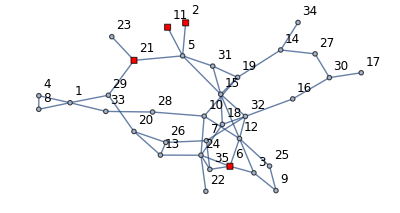

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstanceRG[35, 51, 4, WeightBounds ->{1, 1000}];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12],ImageSize->400]
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_small.mx", {graph15, weightAssociation15, terminals15}];
```

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstanceRG[150, 250, 20, WeightBounds ->{1, 1000}];
```

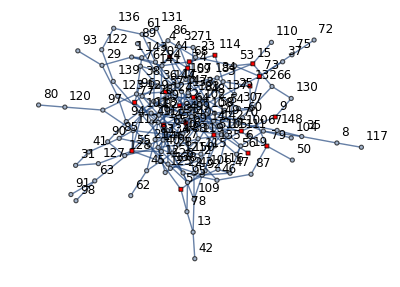

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_medium.mx", {graph100, weightAssociation100, terminals100}];
```

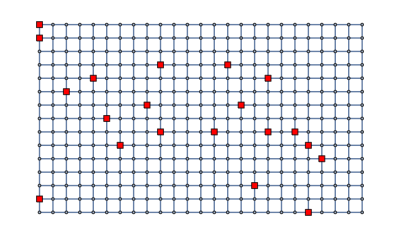

```mathematica
{graphGrid, terminalsGrid} = generateSteinerProblemInstanceGrid[15, 25, 20];
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,12],ImageSize->400, VertexLabels->None]
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_grid.mx", {graphGrid, terminalsGrid}];
```

### SteinLib

```mathematica
getInstancesList["steinlib\\D"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\D\\d20.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

25000

500

```mathematica
getInstancesList["steinlib\\PUC"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\PUC\\bip52p.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

2200

7997

200

## Visualization Examples

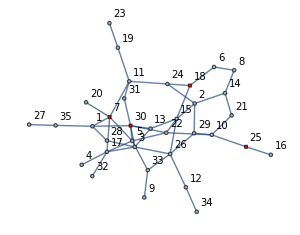

```mathematica
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,10]]
```

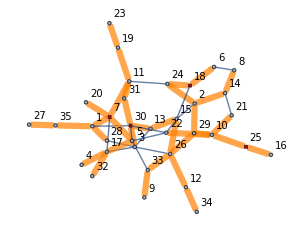

```mathematica
drawGraphSubgraph[graph15, FindSpanningTree[graph15]//EdgeList, terminals15, VertexLabelStyle->Directive[Black,10]]
```

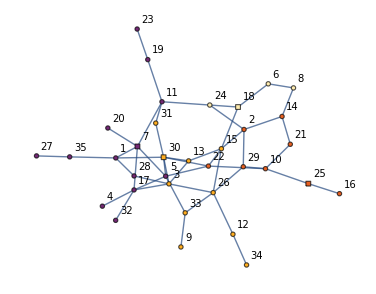

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]],
TerminalSize->0.65]
```

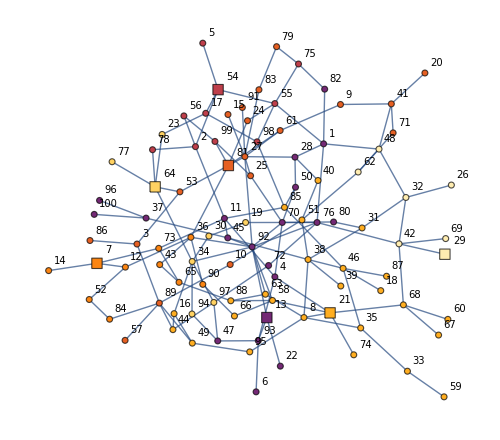

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

### Animation export

```mathematica
dijkstraVoronoi[graph15, terminals15];
voronoiVertexStyle[VertexList@graph15, Normal[%["voronoi"]]]⟦%["order"]⟧;
a = Table[
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧,
TerminalSize->0.65,
ImageSize->500]
,
{step, 1,VertexCount@graph15, 1}];
```

```mathematica
Export["visual/steiner_voronoi.gif", a, "GIF" , "ControlAppearance"->None,"DisplayDurations"->0.5,ImageSize->700];
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description [1]

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2+poly()), where t = #Terminals. n = #Vertices.

#### 15

{0.167622,Null}

1884.

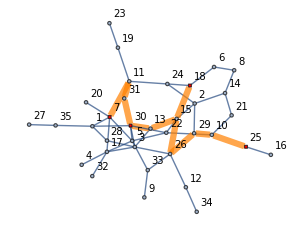
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884.

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
resultDreyfusWagner15
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

#### 100 Verts

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
resultDreyfusWagner100
```

{13.9607,Null}

5933.

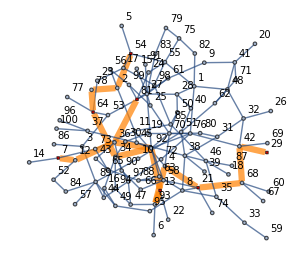
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 5933.

```mathematica
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

#### Stlib

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultDreyfusWagnerStlibTest
```

{0.0491777,Null}

7.

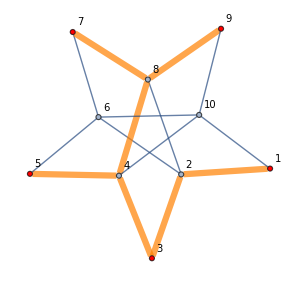
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7.

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagnerStlibTest, stlibTestWeights]
```

7

#### GridGraph

```mathematica
({resultDreyfusWagnerGrid, treeDreyfusWagnerGrid} = runDreyfusWagner[graphGrid, terminalsGrid]);//AbsoluteTiming
resultDreyfusWagnerGrid
steinerSolutionQ[treeDreyfusWagnerGrid, terminalsGrid]
```

{30.4008,Null}

33.

True

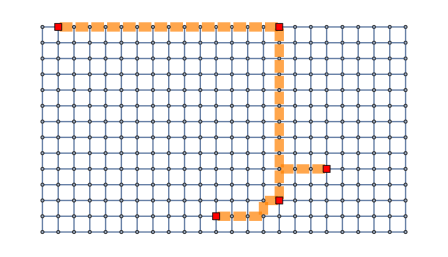
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 542

```mathematica
gridResult[graphGrid, terminalsGrid, treeDreyfusWagnerGrid, resultMehlhornStlibTest, VertexLabels->None]
```

## Voronoi

### Examples

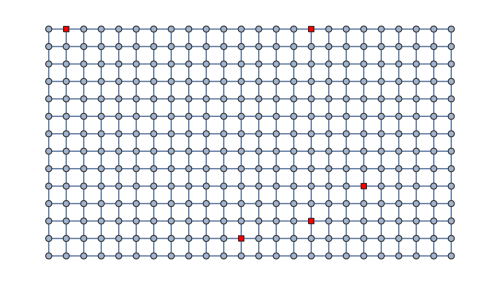

```mathematica
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,10],
TerminalSize->1.25, ImageSize->500, VertexLabels->None, VertexSize->0.35]
```

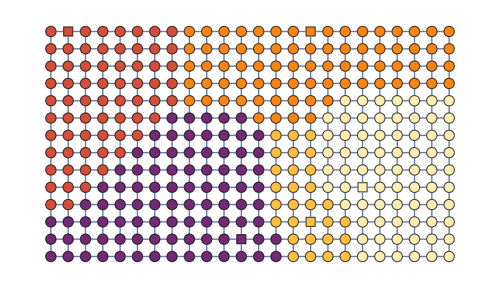

```mathematica
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graphGrid, Normal[dijkstraVoronoi[graphGrid, terminalsGrid]["voronoi"]]],
TerminalSize->1.25, ImageSize->500, VertexLabels->None, VertexSize->0.6]
```

## Leftist Heap

### Examples

```mathematica
ClearAll[a,b,c]
```

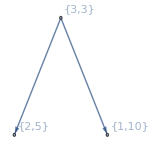
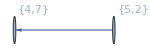

```mathematica
a = leftistHeapHeapify[{{1, 10}, {2, 5}, {3, 3}}];
b = leftistHeapHeapify[{{4, 7}, {5, 2}}];
Row[{leftistHeapDraw[a], leftistHeapDraw[b]}]
```

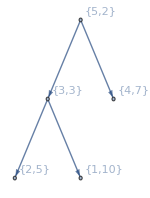

```mathematica
leftistHeapMeldClearly[c,a, b];
leftistHeapDraw[c]
```

5

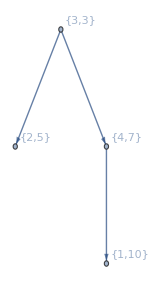

```mathematica
leftistExtractMin@c
leftistHeapDraw[c]
```

```mathematica
ClearAll[a,b,c]
```

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description [1]

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi separation of graph.
	- new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Refind original short-path graph accorgind to spanning tree.
4. Find MinSpanningTree in it.
5. Cut it, to make Steiner-tree.

### Examples

#### 15 Verts

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[graph15, treeKouMarkowskyBerman15]
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

{0.0765441,Null}

1884

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[graph15, treeMehlhorn15]
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

{0.0118319,Null}

1884

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884

#### 100 Verts

{0.139415,Null}

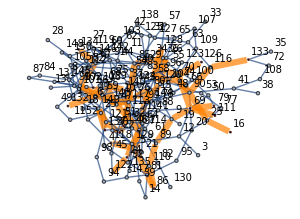
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16083

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[graph100, treeKouMarkowskyBerman100];
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[graph100, treeMehlhorn100];
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

{0.0236352,Null}

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16083

#### Stlib

```mathematica
(treeKouMarkowskyBermanStlibTest = runKouMarkowskyBerman[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultKouMarkowskyBermanStlibTest = edgeWeightSum[stlibTestGraph, treeKouMarkowskyBermanStlibTest]
gridResult[stlibTestGraph,  stlibTestTerminals, treeKouMarkowskyBermanStlibTest, resultKouMarkowskyBermanStlibTest];
```

$Aborted

Total[treeKouMarkowskyBermanStlibTest]

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
steinerSolutionQ[treeMehlhornStlibTest, stlibTestTerminals]
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest];
```

{0.48141,Null}

37452

True

#### GridGraph

{0.0383145,Null}

70

True

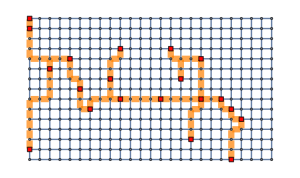
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70

```mathematica
(treeMehlhornGridTest = runMehlhorn[graphGrid, terminalsGrid]);//AbsoluteTiming
resultMehlhornGridTest = edgeWeightSum[graphGrid, treeMehlhornGridTest]
steinerSolutionQ[treeMehlhornGridTest, terminalsGrid]
gridResult[graphGrid, terminalsGrid, treeMehlhornGridTest, resultMehlhornGridTest, VertexLabels->None]
```

## Greedy algorithms [6][7]

### SPH

#### Description

Алгоритм начинает с заданного терминала, и добавляет в дерево текущий близжайший терминал (относительно всех вершин дерева) до тех пор, пока не добавит все терминалы .

### Repeated SPH

#### Description

SPH запускается заданное количество раз из случайного терминала (без повторов), затем берется лучший из результатов.

### Examples

{0.0842098,{30<->13,13<->15,15<->2,18<->24,24<->2,24<->11,2<->29,29<->10,10<->25,11<->7}}

3120

True

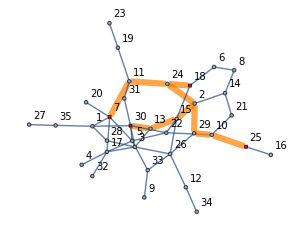
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 3120

```mathematica
(treeRSP15 = steinerRepeatedShortestPathHeuristic[graph15, terminals15, 100])//AbsoluteTiming
resultRSP15 = edgeWeightSum[graph15, treeRSP15]
steinerSolutionQ[treeRSP15, terminals15]
gridResult[graph15,  terminals15, treeRSP15, resultRSP15]
```

{11.1976,Null}

True

18762

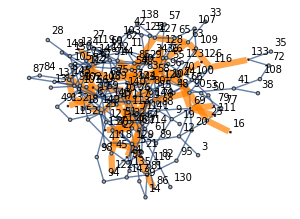
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 18762

```mathematica
(treeSP100 = steinerRepeatedShortestPathHeuristic[graph100, terminals100, 100]);//AbsoluteTiming
steinerSolutionQ[treeSP100, terminals100]
resultSP100 = edgeWeightSum[graph100, treeSP100]
gridResult[graph100,  terminals100, treeSP100, resultSP100]
```

{79.2298,Null}

True

105

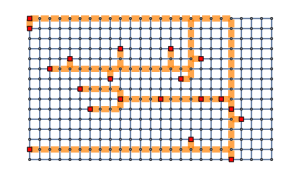
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105

```mathematica
(treeSPGrid = steinerRepeatedShortestPathHeuristic[graphGrid, terminalsGrid, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPGrid, terminalsGrid]
resultSPGrid = edgeWeightSum[graphGrid, treeSPGrid]
gridResult[graphGrid,  terminalsGrid, treeSPGrid, resultSPGrid, VertexLabels->None]
```

## Local-search algorithms [7]

Для любого T - допустимого решения задачи штейнера на графе (не обязательно оптимального) выполняется неравенство MST[V (T)] ≤ T.
Т.е. нахождением минимального остовного дерева набора вершин решения в графе, можно получить тривиальное улучшение решения.
И наоборот, для любого оптимального дерева штейнера должно выполнятся равенство.

### Steiner-Vertex Insertion

#### Description

Steiner-vertex Insertion просматривает окрестность решений, отличающуюся от данного 1-ой добавленной вершиной, пересчитывает для элементов окрестности MST и проверяет, можно ли получить улучшение таким образом.

#### Examples

```mathematica
tree = steinerVertexInsertion[graph15, treeKouMarkowskyBerman15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,11<->31,30<->31,13<->30,18<->24,13<->15,15<->26,2<->24,10<->25,10<->29,26<->29,2<->29}

2173

2173

```mathematica
tree = steinerVertexInsertion[graph100, treeKouMarkowskyBerman100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{117<->136,137<->149,24<->97,47<->97,47<->76,47<->139,76<->80,116<->133,63<->116,63<->127,26<->85,26<->120,26<->58,85<->117,117<->143,80<->93,93<->120,10<->93,22<->129,75<->149,18<->149,139<->140,86<->110,23<->129,89<->110,70<->126,69<->70,70<->96,70<->124,9<->69,69<->111,9<->89,83<->96,96<->104,75<->83,75<->112,44<->124,44<->54,54<->127,45<->122,45<->51,51<->144,90<->144,25<->90,74<->90,48<->104,48<->100,56<->112,16<->25,58<->74,58<->128,17<->132,17<->102,102<->143,67<->102,59<->143,50<->79,50<->100,67<->134,10<->23,2<->23,18<->59,2<->118}

21343

21343

```mathematica
tree = steinerVertexInsertion[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

540

542

```mathematica
tree = steinerVertexInsertionFixedPoint[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

540

542

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]
```

70

70

### Steiner-Vertex Elimination

#### Description

Steiner-vertex Elimination просматривает окрестность решений, отличающуюся от данного 1-ой удаленной вершиной штейнера, и для каждого элемента этой окрестности пересчитывает MST (если он связен), и проверяет, возможно ли улучшение решения.

#### Examples

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

True

1884

2173

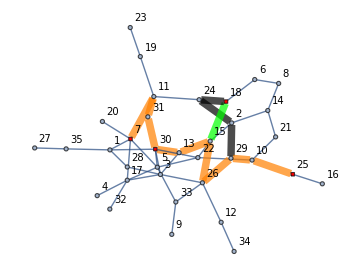
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173→1884

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
gridResultCompare[graph15,  terminals15, tree, treeKouMarkowskyBerman15, edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]->edgeWeightSum[tree, weightAssociation15]]
```

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{9<->69,9<->89,16<->25,17<->102,17<->132,22<->129,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,48<->93,48<->104,51<->144,56<->112,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->116,90<->144,93<->120,96<->104,102<->143,110<->129,116<->133,117<->136,117<->143,118<->129,137<->149,139<->140}

True

17939

21343

```mathematica
tree = steinerVertexEliminationFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{22<->136,22<->121,117<->136,67<->134,67<->102,117<->143,85<->117,102<->143,17<->102,58<->128,26<->58,58<->74,26<->85,26<->120,5<->93,80<->93,93<->120,5<->118,5<->81,81<->86,86<->110,76<->80,47<->76,47<->97,47<->139,47<->56,24<->97,24<->122,139<->140,9<->69,69<->70,69<->79,69<->111,9<->89,89<->110,17<->132,121<->149,137<->149,16<->25,25<->90,74<->90,90<->116,116<->133,70<->96,70<->126}

True

16083

16083

```mathematica
tree = steinerVertexEliminationFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

True

541

542

### VIVE

#### Description

Vertex insertion, vertex elimination

#### Examples

```mathematica
tree =  steinerVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

True

1884

2173

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{9<->69,9<->89,16<->25,17<->102,17<->132,22<->113,22<->129,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->113,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->116,90<->144,93<->120,102<->143,110<->129,113<->140,116<->133,117<->136,117<->143,118<->129,137<->149,139<->140}

True

17075

21343

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{22<->136,22<->121,117<->136,67<->134,67<->102,117<->143,85<->117,102<->143,17<->102,58<->128,26<->58,58<->74,26<->85,26<->120,5<->93,80<->93,93<->120,5<->118,5<->81,81<->86,86<->110,76<->80,47<->76,47<->97,47<->139,47<->56,24<->97,24<->122,139<->140,9<->69,69<->70,69<->79,69<->111,9<->89,89<->110,17<->132,121<->149,137<->149,16<->25,25<->90,74<->90,90<->116,116<->133,70<->96,70<->126}

True

16083

16083

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeSP100, weightAssociation100]
```

{1<->8,1<->23,5<->81,5<->93,5<->118,8<->102,10<->23,10<->93,16<->25,17<->102,17<->132,22<->113,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->83,75<->113,75<->149,76<->80,80<->93,81<->86,83<->96,85<->117,90<->116,90<->144,93<->120,113<->140,116<->133,117<->136,137<->149,139<->140}

True

16725

18762

```mathematica
tree =  steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{22<->136,22<->121,117<->136,67<->134,67<->102,117<->143,85<->117,102<->143,17<->102,58<->128,26<->58,58<->74,26<->85,26<->120,5<->93,80<->93,93<->120,5<->118,5<->81,81<->86,86<->110,76<->80,47<->76,47<->97,47<->139,47<->56,24<->97,24<->122,139<->140,9<->69,69<->70,69<->79,69<->111,9<->89,89<->110,17<->132,121<->149,137<->149,16<->25,25<->90,74<->90,90<->116,116<->133,70<->96,70<->126}

True

16083

16083

103

105

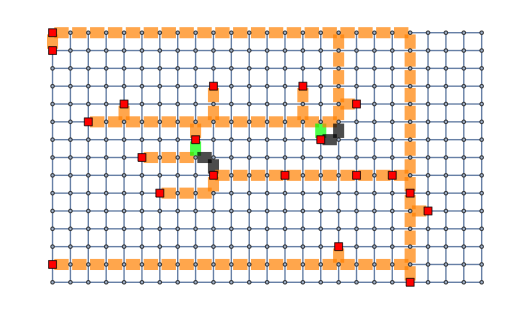
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→103

```mathematica
tree = steinerVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

### Key-Path Exchange

#### Description [7]

Вершина критическая - это либо вершина штейнера степени >= 3, либо терминал . 
Key - path - путь, между двумя критическими вершинами, который не содержит других критических вершин .
Локальный поиск смотрит на каждый key - path и пытается заменить его на другой .

Чтобы считать меньше кратчайших путей, используются диаграммы вороного (dijkstraVoronoi), с центрами во всех вершинах входного дерева, а также хитрый пересчет этих диаграмм (чтобы найти новые граничные ребра при попытке удаления пути).

Зам: Диаграмма вороного - разбиение вершин графа на зоны, относительно заданных центров. Вершина u относится к центру c, если c близжайщий для нее из всех центров. Построение диаграммы вороного реализовано с помощью модифицированного алгоритма Дейкстры. Он запускается одновременно из всех вершин-центров, с общей очередью и массивами длинн путей, предков и посещенности. При этом, дополнительно хранится массив центров (какому центру принадлежит вершина).

Алгоритм: 
Находится диаграмма вороного с центрами в вершинах входного дерева-решения. Для каждой вершины создается левосторонняя куча (leftist heap)(leftistHeapCreate). Для каждого ребра графа, если оно пограничное (его вершины лежат в разных зонах диаграмы), то оно push'ится в кучи, соответствующие центрам зон, с весом равным кратчайшему пути до его концов от центров + вес самого ребра.

Граф подвешивается (rootTree). И затем обходится от листьев к деревьям. После обхода поддерева, кучи в нем сливаются (т.к. теперь поддерево -- не разбиваемо никаким из еще не рассмотренных key-path). При возвращении dfs, вверх передается текущий (потенциальный) key-path, который затем проверяется на возможность замены. Вершины также хранятся в виде СНМ ("DisjointSet"), для определения принадлежности конца ребра поддереву.

```mathematica
-Graphics-
-Graphics-
```

#### Examples

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,15<->18}

1884

2173

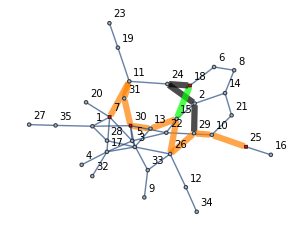
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173→1884

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]

gridResultCompare[graph15,  terminals15, tree, treeKouMarkowskyBerman15, edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]->edgeWeightSum[graph15, tree]]
```

True

16311

21343

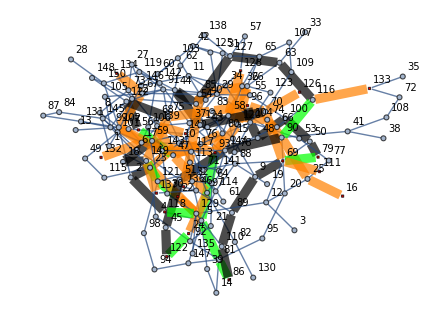
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 21343→16311

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100];
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeKouMarkowskyBerman100]

gridResultCompare[graph100,  terminals100, tree, treeKouMarkowskyBerman100, edgeWeightSum[graph100, treeKouMarkowskyBerman100]->edgeWeightSum[graph100, tree]]
```

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph100, treeMehlhorn100, terminals100];
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

True

15864

16083

```mathematica
(tree =  steinerKeyPathExchange[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{6.93159,Null}

True

542

542

```mathematica
(tree =  steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{27.2326,Null}

True

539

542

### PEVIVE

Vertex insertion, vertex elimination

#### Examples

```mathematica
tree =  steinerPEVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,15<->18}

True

1884

2173

{5<->81,5<->93,5<->118,16<->25,17<->102,17<->132,22<->121,22<->136,24<->97,24<->122,25<->90,26<->58,26<->85,26<->120,47<->56,47<->76,47<->97,47<->139,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,76<->80,80<->93,81<->86,85<->117,90<->116,93<->120,102<->143,116<->133,117<->136,117<->143,121<->149,137<->149,139<->140,12<->25,12<->69}

True

15864

21343

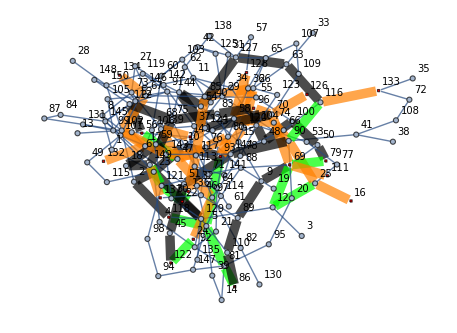
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 21343→15864

```mathematica
tree =  steinerPEVIVEFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]

gridResultCompare[graph100,  terminals100, tree, treeKouMarkowskyBerman100, edgeWeightSum[graph100, treeKouMarkowskyBerman100]->edgeWeightSum[graph100, tree]]
```

```mathematica
tree =  steinerPEVIVEFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{5<->81,5<->93,5<->118,16<->25,17<->102,17<->132,22<->121,22<->136,24<->97,24<->122,25<->90,26<->58,26<->85,26<->120,47<->56,47<->76,47<->97,47<->139,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,76<->80,80<->93,81<->86,85<->117,90<->116,93<->120,102<->143,116<->133,117<->136,117<->143,121<->149,137<->149,139<->140,12<->25,12<->69}

True

15864

18762

```mathematica
edgeWeightSum[graph100, treeMehlhorn100]
```

16083

```mathematica
tree =  steinerPEVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]
```

{5<->81,5<->93,5<->118,16<->25,17<->102,17<->132,22<->113,24<->97,25<->90,26<->58,26<->85,26<->120,47<->56,47<->76,47<->97,47<->139,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->83,75<->113,75<->149,76<->80,80<->93,81<->86,83<->96,85<->117,90<->116,93<->120,102<->143,113<->140,117<->136,117<->143,133<->116,137<->149,139<->140,24<->122}

True

15881

18762

```mathematica
(tree =  steinerPEVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{36.1815,Null}

True

539

542

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

### Examples

#### Grid graph

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeSPGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]
```

105

105

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]
```

70

70

103

105

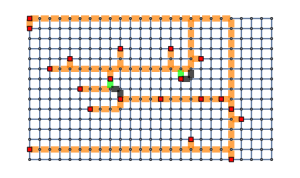
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→103

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

67

70

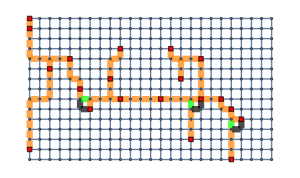
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→67

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

68

105

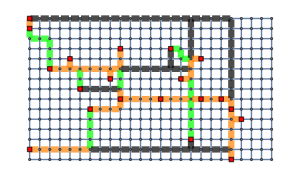
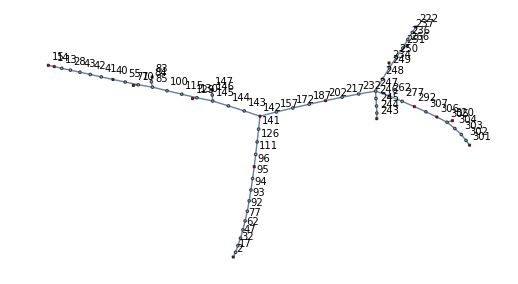
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→68

```mathematica
tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

```mathematica
gridMelhornFrames = (drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]&/@
Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest}}, Reap[steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧]);
```

```mathematica
Export["visual/key_path_exchange_grid_mehlhorn.gif", gridMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

{1.34462,Null}

True

66

70

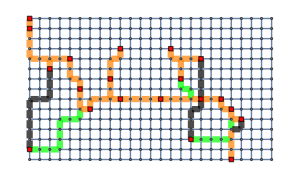
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→66

```mathematica
(tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid]);//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

69

105

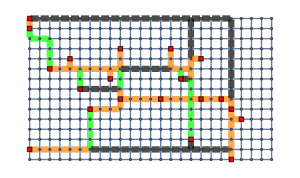
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→69

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

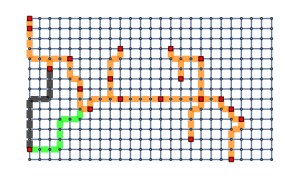
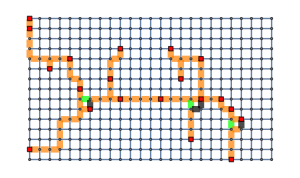
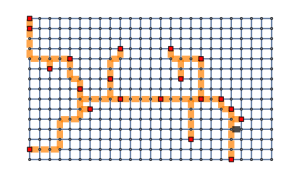
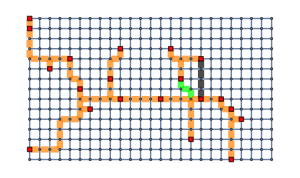
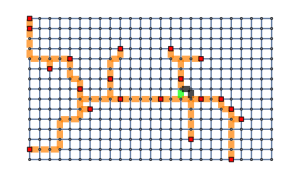
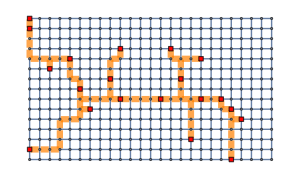
{-Graphics-
START,-Graphics-
PE,-Graphics-
VE,-Graphics-
VE,-Graphics-
PE,-Graphics-
VE,-Graphics-
PE}

```mathematica
gridPEVIVEMelhornFramesReap = Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest, "START"}}, Reap[steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧];

gridPEVIVEMelhornFrames = Grid[{{drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]}, {#⟦3⟧}}]&/@gridPEVIVEMelhornFramesReap
```

```mathematica
Export["visual/pevive_grid_mehlhorn.gif", gridPEVIVEMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

{3.18337,Null}

True

65

70

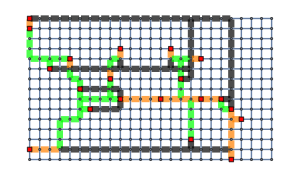
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→65

```mathematica
(tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];)//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

## Computations

### Random

```mathematica
test1=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{10, 15, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{10,15,3,WeightBounds→{1,100000}}},0.0060138},{{{PLCHDR,PLCHDR},{10,15,4,WeightBounds→{1,100000}}},0.0185274},{{{PLCHDR,PLCHDR},{10,15,5,WeightBounds→{1,100000}}},0.0517515},{{{PLCHDR,PLCHDR},{10,15,6,WeightBounds→{1,100000}}},0.114701},{{{PLCHDR,PLCHDR},{10,15,7,WeightBounds→{1,100000}}},0.270782}}

```mathematica
test2=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{100, 150, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{100,150,3,WeightBounds→{1,100000}}},0.599665},{{{PLCHDR,PLCHDR},{100,150,4,WeightBounds→{1,100000}}},1.27461},{{{PLCHDR,PLCHDR},{100,150,5,WeightBounds→{1,100000}}},2.94726},{{{PLCHDR,PLCHDR},{100,150,6,WeightBounds→{1,100000}}},6.49862},{{{PLCHDR,PLCHDR},{100,150,7,WeightBounds→{1,100000}}},14.6351}}

```mathematica
DumpSave[Directory[]~~"/dump/test_data.mx", {test1, test2}];
```

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {15, 3, BernoulliProbability->0.125}, 100, False]
```

0.0128711

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {100, 7, BernoulliProbability->0.1}, 1, False]
```

14.2756

```mathematica
testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {{15, 3, BernoulliProbability->0.125}, {50, 5, BernoulliProbability->0.08}, {100, 7, BernoulliProbability->0.05}}, 1, False]
```

{{{{PLCHDR,PLCHDR},{15,3,BernoulliProbability→0.125}},0.011905},{{{PLCHDR,PLCHDR},{50,5,BernoulliProbability→0.08}},0.760988},{{{PLCHDR,PLCHDR},{100,10,BernoulliProbability→0.05}},183.929}}

### SteinLib import

```mathematica
getInstancesList["\\steinlib\\D"];
```

```mathematica
getInstancesList["steinlib\\D"]
```

{steinlib\D\d01.stp,steinlib\D\d02.stp,steinlib\D\d03.stp,steinlib\D\d04.stp,steinlib\D\d05.stp,steinlib\D\d06.stp,steinlib\D\d07.stp,steinlib\D\d08.stp,steinlib\D\d09.stp,steinlib\D\d10.stp,steinlib\D\d11.stp,steinlib\D\d12.stp,steinlib\D\d13.stp,steinlib\D\d14.stp,steinlib\D\d15.stp,steinlib\D\d16.stp,steinlib\D\d17.stp,steinlib\D\d18.stp,steinlib\D\d19.stp,steinlib\D\d20.stp}

```mathematica
steinLibInstancesDList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\D"])⟦All, {1,3}⟧;
```

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D.mx", {steinLibInstancesDList}];
```

```mathematica
<<"/dump/steinlib_D.mx"
```

```mathematica
(*(steinLibInstancesDKou = tester[runKouMarkowskyBerman, steinLibInstancesDList, 10, First]);//AbsoluteTiming*)
```

```mathematica
(steinLibInstancesDMehlhorn = tester[runMehlhorn, steinLibInstancesDList, 1, First]);//AbsoluteTiming
```

{334.585,Null}

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D_sol.mx", {steinLibInstancesDMehlhorn}];
```

```mathematica
steinLibInfoD = Import["steinlib\\D_info.xlsx", "Data"]⟦1⟧;
steinLibInfoD = AssociationThread[Rest@First[steinLibInfoD], #]&/@Association[StringTrim[First[#]]->Rest[#]&/@Rest[steinLibInfoD]]
```

<|d01→<|vertices→1000 ,edges→1250 ,terminals→5 ,hardness→Ps ,opt→106 |>,d02→<|vertices→1000 ,edges→1250 ,terminals→10 ,hardness→Ps ,opt→220 |>,d03→<|vertices→1000 ,edges→1250 ,terminals→167 ,hardness→Ps ,opt→1565 |>,d04→<|vertices→1000 ,edges→1250 ,terminals→250 ,hardness→Ps ,opt→1935 |>,d05→<|vertices→1000 ,edges→1250 ,terminals→500 ,hardness→Ps ,opt→3250 |>,d06→<|vertices→1000 ,edges→2000 ,terminals→5 ,hardness→Ps ,opt→67 |>,d07→<|vertices→1000 ,edges→2000 ,terminals→10 ,hardness→Ps ,opt→103 |>,d08→<|vertices→1000 ,edges→2000 ,terminals→167 ,hardness→Ps ,opt→1072 |>,d09→<|vertices→1000 ,edges→2000 ,terminals→250 ,hardness→Ps ,opt→1448 |>,d10→<|vertices→1000 ,edges→2000 ,terminals→500 ,hardness→Ps ,opt→2110 |>,d11→<|vertices→1000 ,edges→5000 ,terminals→5 ,hardness→Pm ,opt→29 |>,d12→<|vertices→1000 ,edges→5000 ,terminals→10 ,hardness→Pm ,opt→42 |>,d13→<|vertices→1000 ,edges→5000 ,terminals→167 ,hardness→Ps ,opt→500 |>,d14→<|vertices→1000 ,edges→5000 ,terminals→250 ,hardness→Ps ,opt→667 |>,d15→<|vertices→1000 ,edges→5000 ,terminals→500 ,hardness→Ps ,opt→1116 |>,d16→<|vertices→1000 ,edges→25000 ,terminals→5 ,hardness→Pm ,opt→13 |>,d17→<|vertices→1000 ,edges→25000 ,terminals→10 ,hardness→Pm ,opt→23 |>,d18→<|vertices→1000 ,edges→25000 ,terminals→167 ,hardness→Ps ,opt→223 |>,d19→<|vertices→1000 ,edges→25000 ,terminals→250 ,hardness→Ps ,opt→310 |>,d20→<|vertices→1000 ,edges→25000 ,terminals→500 ,hardness→Ls ,opt→537.|>|>

```mathematica
#["opt"]&/@Values[steinLibInfoD]
```

{106 ,220 ,1565 ,1935 ,3250 ,67 ,103 ,1072 ,1448 ,2110 ,29 ,42 ,500 ,667 ,1116 ,13 ,23 ,223 ,310 ,537.}

```mathematica
steinLibInstancesDKou⟦All, 2, 1⟧
```

```mathematica
steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDVert = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
steinLibDEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoD])
steinLibDTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

{1250,1250,1250,1250,1250,2000,2000,2000,2000,2000,5000,5000,5000,5000,5000,25000,25000,25000,25000,25000}

{5,10,167,250,500,5,10,167,250,500,5,10,167,250,500,5,10,167,250,500}

```mathematica
steinLibDOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

```mathematica
steinLibDMehlhornTime  = steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhorn⟦All, 2, 2⟧}]
```

{107,237,1608,1978,3263,73,105,1125,1513,2133,31,42,524,690,1137,15,25,248,335,542}

```mathematica
steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhorn⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
steinLibDMehlhornSolErr = N@Thread[Divide[(steinLibDMehlhornSolValues-steinLibDOpt), steinLibDOpt]]
```

{0.00943396,0.0772727,0.027476,0.0222222,0.004,0.0895522,0.0194175,0.0494403,0.0448895,0.0109005,0.0689655,0.,0.048,0.0344828,0.0188172,0.153846,0.0869565,0.112108,0.0806452,0.00931099}

```mathematica
Grid[Transpose[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн", "%Ошибки ^-3", "Время (сек.)"}}~Join~(Transpose[{Keys@steinLibInfoD, steinLibDVert, steinLibDEdges, steinLibDTerm, steinLibDOpt, steinLibDMehlhornSolValues,Round[steinLibDMehlhornSolErr, N@10^-3], Round[steinLibDMehlhornTime, N@10^-1]}]⟦{1, 5, 10, 15, 19, 20}⟧)~Join~{{"Среднее", "-", "-", "-", "-", "-", Round[Mean@steinLibDMehlhornSolErr, N@10^-3], Round[Mean@steinLibDMehlhornTime, N@10^-1]}}],
Frame->All]
```

Задача | d01 | d05 | d10 | d15 | d19 | d20 | Среднее
#Вершин | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
#Ребер | 1250 | 1250 | 2000 | 5000 | 25000 | 25000 | -
#Терминалов | 5 | 500 | 500 | 500 | 250 | 500 | -
Оптимальное | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
Мельхорн | 107 | 3263 | 2133 | 1137 | 335 | 542 | -
%Ошибки ^-3 | 0.009 | 0.004 | 0.011 | 0.019 | 0.081 | 0.009 | 0.048
Время (сек.) | 0.1 | 0.8 | 0.7 | 2.4 | 89.8 | 73.9 | 16.7

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper

539

542